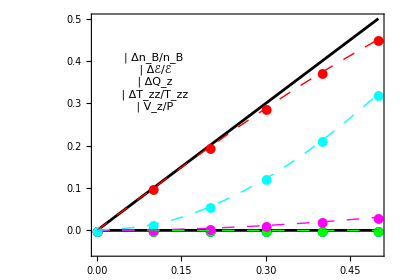

```mathematica
(* Subscript[V, z] *)

(*LHC Pb+Pb 5.02 TeV*)

T = 158.4;
μB =0.90; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

ΔQzdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.0013047,0.005184,0.011538,0.020211,0.031011};

ΔTzzoverTzzdata = {0.0,0.014024,0.055455,0.12247,0.21234,0.32181};

VzaBovernBdata = {0.0,0.09955,0.19646,0.28841,0.37361,0.45093};



style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};



legend1=Panel[Grid[{{Graphics[{Blue,Disk[]},ImageSize->10],Style["Δn_B/n_B",FontSize->18,FontFamily->"Times"]},{Graphics[{RGBColor[1,0,1],Disk[]},ImageSize->10],Style["Δℰ/ℰ",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[0,1,0],Disk[]},ImageSize->10],Style["ΔQ_z",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[0,1,1],Disk[]},ImageSize->10],Style["ΔT_zz/T_zz",FontSize->18,FontFamily->"Times"]},
{Graphics[{RGBColor[1,0,0],Disk[]},ImageSize->10],Style["V_z/P",FontSize->18,FontFamily->"Times"]}}],Background->White];

legend3=Panel[Grid[{{Style["LHC Pb+Pb   √s = 5.02 TeV",FontSize->16,FontFamily->"Times"]}}],Background->White];


legend2=Panel[Grid[{{Style["T_CF = 158.4 MeV",FontSize->16,FontFamily->"Times"]},{},{Style["μ_B = 0.9 MeV",FontSize->16,FontFamily->"Times"]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
ΔQzplot = Table[{frac[[i]],ΔQzdata[[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];
VzaBovernBdataplot  = Table[{frac[[i]],VzaBovernBdata [[i]]},{i,1,Length[frac]}];


pi1=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7],ListLinePlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.1,0.35}]},ImageSize->{400,300}]
```

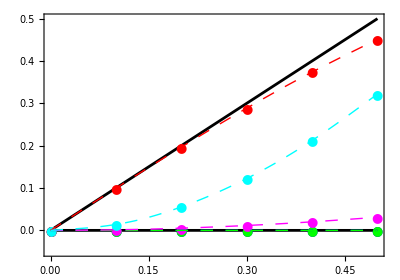

```mathematica
T = 158.384;
μB =22.3; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

ΔQzdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.0013027,0.0051762,0.011522,0.020186,0.030979};

ΔTzzoverTzzdata = {0.0,0.014011,0.055409,0.12239,0.21226,0.32178};

VzaBovernBdata = {0.0,0.099554,0.19649,0.28851,0.37384,0.45134};



style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
ΔQzplot = Table[{frac[[i]],ΔQzdata[[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];
VzaBovernBdataplot  = Table[{frac[[i]],VzaBovernBdata [[i]]},{i,1,Length[frac]}];


pi2=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7],ListLinePlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},ImageSize->{400,300}]
```

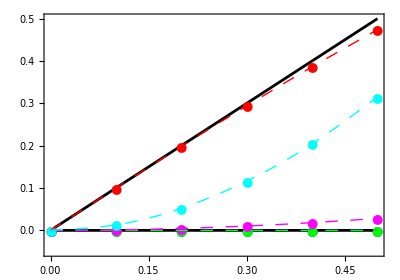

```mathematica
T = 154.7;
μB =218.6; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

ΔQzdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.001154,0.0046034,0.010306,0.018197,0.028193};

ΔTzzoverTzzdata = {0.0,0.013108,0.052152,0.11632,0.20435,0.31467};

VzaBovernBdata = {0.0,0.099771,0.19819,0.29401,0.38617,0.47388};



style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
ΔQzplot = Table[{frac[[i]],ΔQzdata[[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];
VzaBovernBdataplot  = Table[{frac[[i]],VzaBovernBdata [[i]]},{i,1,Length[frac]}];


pi3=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7],ListLinePlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},ImageSize->{400,300}]
```

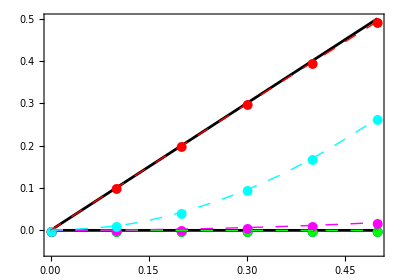

```mathematica
T = 115.1;
μB =535.9; 

frac=Table[0.1*i,{i,0,5}];

ΔnBovernBdata = {0.0,0.0,0.0,0.0,0.0,0.0};

ΔQzdata = {0.0,0.0,0.0,0.0,0.0,0.0};

Δϵoverϵdata = {0.0,0.00073946,0.0029538,0.0066309,0.011751,0.018286};

ΔTzzoverTzzdata = {0.0,0.01073,0.042828,0.096021,0.16986,0.26375};

VzaBovernBdata = {0.0,0.099946,0.19957,0.29856,0.3966,0.49343};



style={Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]],Directive[RGBColor[0,0,0],AbsoluteThickness[2],Dashing[None]]};

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔnBovernBplot = Table[{frac[[i]],ΔnBovernBdata[[i]]},{i,1,Length[frac]}];
ΔQzplot = Table[{frac[[i]],ΔQzdata[[i]]},{i,1,Length[frac]}];
ΔTzzoverTzzplot = Table[{frac[[i]],ΔTzzoverTzzdata[[i]]},{i,1,Length[frac]}];
VzaBovernBdataplot  = Table[{frac[[i]],VzaBovernBdata [[i]]},{i,1,Length[frac]}];


pi4=Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.05,0.5},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"V_zT/(n_Bμ_B)"}],
ListPlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},Frame->True,Axes->False,PlotMarkers->{{●,13},{●,13},{●,13}},PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"V_zT/(n_Bμ_B)"}],ListLinePlot[{ΔnBovernBplot,ΔQzplot,Δϵoverϵplot,VzaBovernBdataplot,ΔTzzoverTzzplot},PlotRange->{-0.05,0.5},InterpolationOrder->2,Frame->True,Axes->False,PlotStyle->{{Blue,Thick,Dashing[Medium]},{RGBColor[0,1,0],Thick,Dashing[Medium]},{RGBColor[1,0,1],Thick,Dashing[Medium]},{RGBColor[1,0,0],Thick,Dashing[Medium]},{RGBColor[0,1,1],Thick,Dashing[Medium]}},BaseStyle->{FontSize->18},AspectRatio->0.7,FrameLabel->{"V_zT/(n_Bμ_B)"}]}
},ImageSize->{400,300}]
```

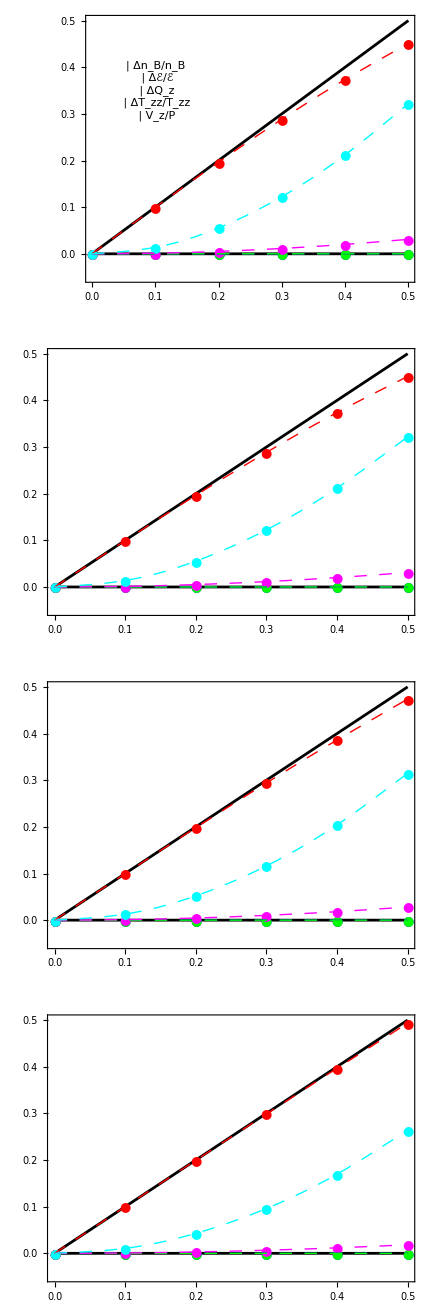

Vtotal.pdf

```mathematica
Vtotal=GraphicsGrid[{{pi1},{pi2},{pi3},{pi4}}]

Export["Vtotal.pdf",pitotal]
```